# Supplementary material: Niche expansion via acquired metabolism facilitates competitive dominance in planktonic communities

## Veronica Hsu, Ferdinand Pfab, Holly V Moeller Contact for code: ferdinand.pfab@gmail.com This file contains the model definitions, the algorithms to fit the model, and the plotting of the simulations.

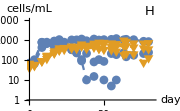

```mathematica
(*Import data*)
dat=Import[NotebookDirectory[]<>"Pbur_Colp_v1.csv","Dataset","HeaderLines"->1];
(*Directory for exporting plots*)
outputdirectory=NotebookDirectory[];
(*By what the time series in the data are defined*)
criteria={"Treatment","Light_Level","Species","Replicate"};
(*get all possibilities for criteria, exclude derived quantities in the data sheet*)
choices[criterion_]:=Complement[Union@Normal@dat[All,criterion],Piecewise[{{{"Colp_Tukey","P bur_Tukey"}, criterion=="Species"}, {{"Colp Control","P. bur Control","Colp Competition","P. bur Competition"}, criterion=="Treatment"}, {{}, True}}]];
(*Function to get time series*) 
gettreatreplicates[type_]:=With[{slots=Slot/@criteria},Normal@dat[Select[slots==type&]][All,{#"Experimental_Day",#"Cells/mL"}&]];
(*function to choose only datapoints with time ≤ tmax*)
croptime[list_,tmax_]:=Select[list,#[[1]]≤tmax(*∧#[[2]]>0*)&];
(*load all replicates give treatment, light and species*)
gettreat[{treatment_,light_,species_}]:=Flatten[Table[gettreatreplicates[{treatment,light,species,replicate}],{replicate,choices["Replicate"]}],1];
(*function to choose only datapoints with time ≤ tmax*)
croptime[list_,tcropped_]:=Select[list,#[[1]]≤tcropped&];
tcropped=50;
gettreatcroptime[type_]:=croptime[gettreat[type],tcropped];
(*letters for the state variables for the species densities*)
speciescodes={"Colp"->c,"P bur"->p};
(*extract trajectories with names of state variables*)
gettreatcroptimewithspecies[type_]:=Table[{species/.speciescodes,gettreatcroptime[Join[type,{species}]]},{species,choices["Species"]}];
(*max time point to show*)
tmaxplot=50;
(*max y axis for plots*)
maxdensity=8000;
(*some style for the plots*)
fontfamily="Arial";
plotmarkerstyles={{1,9},{5,11.5}};
treatnames={"Colp"->Row[{Style["Colpidium",Italic]," alone"}],"Comp"->Column[{"Both species competing"},Alignment->Center],"P bur"->Row[{Style["P. bursaria",Italic]," alone"}]};
(*lines for legen*)
(*replace by second legend definition?*)
legendfits[i_]:=ListPlot[{{-.5,.48},{.47,.48},{1.5,.48}},Joined->True,PlotMarkers->{Graphics`PlotMarkers[]⟦#⟦1⟧,1⟧,1.095#⟦2⟧}&@(plotmarkerstyles[[i]]),PlotStyle->{Dashing[.13],Thick,ColorData[97][i]},PlotRange->{{0,1},{0,1}},Axes->None,ImageSize->25];
(*initial densities for different treatments*)
inis[treatment_]:=Piecewise[{{{p0->50,c0->0}, treatment=="P bur"}, {{c0->50,p0->0}, treatment=="Colp"}, {{p0->50,c0->50}, treatment=="Comp"}}];
testparspre2[model_]:=MapAt[#/.Flatten@testparspre[model]&,testparspre[model],{All,2}];
pars[model_]:=testparspre2[model][[All,1]];
testpars[model_]:=Flatten[testparspre2[model]];
parsbyexperiment[model_,parvalues_,fixedpars_][treatment_,light_]:=pars[model]/.{
c0->Piecewise[{{0, treatment=="P bur"}, {c0, True}}],p0->Piecewise[{{0, treatment=="Colp"}, {p0, True}}],l->light}/.
(#->(#/.parvalues)&/@fixedpars)(*(#->(#/.testpars[model])&/@parskeep[model])*);
parstofit[model_]:=pars[model]/.(#->Nothing&/@Join[parskeep[model],{l}]);

(*get different experiment identifications*)
{lights,treatments,species,replicates}=Union@Normal@Flatten@dat[All,#]&/@{#"Light_Level"&,#"Treatment"&,#"Species"&,#"Replicate"&};
treatments=Complement[treatments,{"Colp Control","P. bur Control","Colp Competition","P. bur Competition"}];
species=Complement[species,{"Colp_Tukey","P bur_Tukey"}];
(*labels for plots given treatment and light level*)
panellabels=#[[1]]->#[[2]]&/@Transpose[{Flatten[Table[{treat,light},{light,lights},{treat,treatments}],1],{"A","B","C","D","E","F","G","H","I","J","K","L"}}];
(*plot data for given treatment and light level*)
plotdataplanestyle[treatment_,light_]:={AxesLabel->{"day","cells/mL"},ImageSize->Small,Epilog->Inset[Style[{treatment,light}/.panellabels,13],Scaled[{.95,1.08}]],PlotRangeClipping->False};
plotdataplane[{treatment_,light_}]:=ListLogPlot[Flatten[Table[Table[Select[croptime[gettreatreplicates[{treatment,light,species,replicate}],tcropped],#1⟦2⟧≠0&],{replicate,choices["Replicate"]}],{species,choices["Species"]}],1]/.{}->{{0,0}},Joined->True,PlotMarkers->Flatten[Table[Table[{Graphics`PlotMarkers[]⟦i⟦1⟧,1⟧,i⟦2⟧},3],{i,plotmarkerstyles}],1],PlotStyle->Flatten[Table[Table[{Dashing[.022],ColorData[97][i]},3],{i,2}],1],PlotRange->{{0,tmaxplot},{10^0,10^4}},Evaluate@plotdataplanestyle[treatment,light]];
plotdataplane[{treatments[[2]],lights[[3]]}]
```

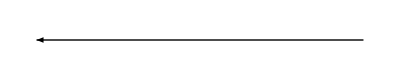
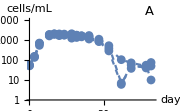
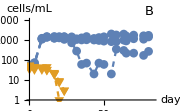
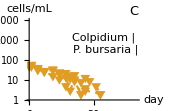
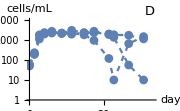
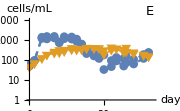
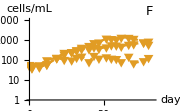
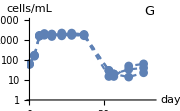
Increasing light intensity, μmol quanta m^-2 s^-1
-Graphics-        |  | Colpidium alone | Both species competing | P. bursaria alone
0 |   | -Graphics- | -Graphics- | -Graphics-
50 |   | -Graphics- | -Graphics- | -Graphics-
100 |   | -Graphics- | -Graphics- | -Graphics-
200 |   | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*do plots with data and simulations, model=string that defines which model is used, parvals=parameter values for simulations*)
plots[model_,parvals_]:=Style[
Row[{
Rotate[Column[{Style[Row[{"Increasing light intensity, μmol quanta m^-2 s^-1"}],FontFamily->fontfamily,14],
Style[Row[{ Graphics[{Thick,Arrowheads->Medium,Arrow[{{2.18,0},{1,0}}]},PlotRange->{-.02,.02},ImageSize->{Automatic,12}],"      "}],FontFamily->fontfamily,14]},Alignment->Center],π/2]," ",

Grid[Join[{Join[{"",""},choices["Treatment"]/.treatnames]},
Table[
Join[{Style[light,14,FontFamily->fontfamily]," "},Table[Show[{
plotdataplane[{treatment,light}],
With[{sol=sim[model][pars[model]/.Join[{l->light},inis[treatment],parvals],tmaxplot]},
LogPlot[Evaluate[{c[t],p[t]}/.sol],{t,0,tcropped},PlotRange->Full,PlotStyle->Thick]]
},
If[TrueQ[treatment=="P bur"∧light==0],Prolog->Inset[Framed[Style[Grid[{{"StyleBox[\"Colpidium\",FontSlant->\"Italic\"]",legendfits[1]},{"StyleBox[\"P\",FontSlant->\"Italic\"]StyleBox[\".\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"bursaria\",FontSlant->\"Italic\"]",legendfits[2]}}],12],RoundingRadius->3],Scaled[{.7,.7}]],{}],PlotRangeClipping->{{True,True},{False,False}}
],{treatment,choices["Treatment"]}
]],{light,choices["Light_Level"]}]],Spacings->{.3,{.3,1,.3,.3,.3}}(*,Frame->True*)]}],FontFamily->fontfamily];
(*put together maximum likelihood function and fitting routine*)
(*plot data on it's own*)
(*(Export[outputdirectory<>"data.svg",#];#)&@*)Quiet@plots["",""]
```

```mathematica
(*models and fitting*)
(*add "shift" to densities to allow log-transpose and make fits less sensible at low densities*)
shift=1;
(*sum square errors: fdatlist=data points (together with species character), sim=simulation, log=do log transform when True*) 
q[pars_?(AllTrue[Flatten@#,NumericQ]&),fdatlist_,sim_,log_]:=With[
{
sol=sim[pars]
},
(**)
Sum[If[Length[fd[[2]]]≥1,
Sum[Re@If[log,(Log[shift+Max[0,d[[2]]]]-Log[shift+Max[0,fd[[1]][d[[1]]]/.sol]])^2,(d[[2]]-(fd[[1]][d[[1]]]/.sol))^2],{d,fd[[2]]}],0
],{fd,fdatlist}]
];

(*function to join parameters that have been fitted and parameters that have been defined otherwise*)
rejoinpars[parssome_,parsall_,parsexclude_]:=Join[parssome,Select[parsall,Not[MemberQ[Join[parssome[[All,1]],parsexclude],#[[1]]]]&]];
(*number of data points for AIC*)
length=Length[Flatten[Table[Table[gettreatcroptime[{treatment,l,specie}],{specie,species}],{treatment,treatments},{l,lights}],3]];
(*functions for fits when using all data together*)
(*joint likelihood*)
jointq[model_,parvalues_,fixedpars_,log_]:=N@Sum[N@q[parsbyexperiment[model,parvalues,fixedpars][treatment,l],
Table[{specie/.speciescodes,gettreatcroptime[{treatment,l,specie}]},{specie,species}],
sim[model][#,tcropped]&,log],{treatment,treatments},{l,lights}];
(*fit model, give max likelihood parameters and AIC*)
fit[model_,conditions_,parstofit_,fixedpars_,inivals_,log_]:=NMinimize[Flatten@{jointq[model,inivals,fixedpars,log],conditions},With[{val=.8#/.inivals},{#,Min[.8val,1.5val],Max[.8val,1.5val]}]&/@Flatten@parstofit,MaxIterations->10^6,
Method->{"NelderMead","PostProcess"->False}];
(*fit[model_,conditions_,parstofit_,fixedpars_,inivals_,log_]:=NMinimize[Flatten@{jointq[model,inivals,fixedpars,log],conditions},With[{val=.8#/.inivals},{#,Min[.8val,1.5val],Max[.8val,1.5val]}]&/@Flatten@parstofit(*,MaxIterations->10^5,
Method->{"NelderMead","PostProcess"->False}*)];*)
aic[ssq_,length_,parnumber_]:=2parnumber+length(1+Log[2 π ssq/length]);
(*for caluclating R^2*)
R2[ssq_,sst_]:=1-ssq/sst;
(*sum of squares Subscript[Sum, i] (Subscript[y, i]-ybar)^2 for calculating R^2, for given treatment, light and species*) 
SStotsingle[type_,log_]:=Module[{dat=Piecewise[{{Log[#+shift], log}, {#, True}}]&/@gettreatcroptime[type][[All,2]],ybar},
If[Length[dat]==0,
0,
ybar=Mean[dat];
Sum[(ybar-y)^2,{y,dat}]]
];
(*total sum of squares for calculating R^2*) 
SStot[log_]:=Total@Flatten@Table[SStotsingle[{treatment,light,specie},log],{treatment,treatments},{light,lights},{specie,species}]
```

```mathematica
(*functions for fits when doing two stage fit: first single experiments, then competition*)
fitStages[model_,log_,treatmentsANDlights_,maxday_,initialpars_,parstofit_,conditions_]:=
Module[{nminimize,jointq},
jointq=Sum[
Module[{treatment,light},
{treatment,light}=treatlight;
q[pars[model]/.{
c0->Piecewise[{{0, treatment=="P bur"}, {c0, True}}],p0->Piecewise[{{0, treatment=="Colp"}, {p0, True}}],l->light}/.Select[initialpars,Not@MemberQ[parstofit,#[[1]]]&],
Table[{specie/.speciescodes,gettreatcroptime[{treatment,light,specie}]},{specie,species}],
sim[model][#,tcropped]&,log]],
{treatlight,treatmentsANDlights}];
NMinimize[Flatten@{jointq,conditions},With[{val=.8#/.testpars[model]},{#,Min[.8val,1.5val],Max[.8val,1.5val]}]&/@Flatten@parstofit,MaxIterations->10^5,Method->{"NelderMead","PostProcess"->False}]];
joinpars[old_,new_]:=Join[new,Select[old,Not@MemberQ[new[[All,1]],#[[1]]]&]];
```

```mathematica
(*define the simplified mechanistical model*)
model="mech-simple";
(*state variables*)
vars[model]={c,p,b1,b2};
(*define and run the model*)
sim[model][{
c0_,ac1_,ac2_,hc_,mc_,
p0_,ap1_,ap2_,hp_,mp_,
yc_,yp_,
w1_,w2_,δ_,
k_,l_
},tmax_]:=Module[{g,f,h,uc,ucs,lc,up,ups,lp,ub1,uc1,up1,ub2,uc2,up2},
f[a_,h_][x_]:=(a  x)/(1+a h x);
h[a1_,a2_,h_][x1_,x2_][y1_,y2_]:=(a1 y1+a2 y2)/(1+a1 h x1+a2 h x2);
ub1=w1;
ub2=w2;
uc1=h[ac1,ac2,hc][b1[t],b2[t]][b1[t],0] c[t];
uc2=h[ac1,ac2,hc][b1[t],b2[t]][0,b2[t]] c[t];
uc=uc1+uc2;
lc=mc c[t];
up1=h[ap1,ap2,hp][b1[t],b2[t]][b1[t],0] p[t];
up2=h[ap1,ap2,hp][b1[t],b2[t]][0,b2[t]] p[t];
up=up1+up2;
lp=(1-l/(l+k))mp p[t];
NDSolve[
{
b1'[t]==ub1-uc1-up1-δ b1[t],
b2'[t]==ub2-uc2-up2-δ b2[t],
c'[t]==yc uc-lc,
p'[t]==yp up-lp,
c[0]==c0,
p[0]==p0,
b1[0]==w1/δ,
b2[0]==w2/δ
},
vars[model],
{t,0,tmax},MaxSteps->Infinity,Method->"Shooting"][[1]]];
(*parameters to initialize fitting*)
testparspre[model]={
c0->50,ac1->0.00013879760699376506,ac2->0.0020860992269208845,hc->9.043295525612516*^-8 ,mc->0.42771939139856185,
p0->50,ap1->0.0011245238856716962,ap2->0.0002486418989610944,hp->2.7705020433589733*^-7,mp->0.4750306312284005,
yc-> 10^-7,yp->10^-7,
w1->10^9,w2-> 10^9 ,δ->0.01596951008564933,k->75.08950776567782,l->50};
(*parameters no to fit*)
parskeep[model]={c0,p0,yc,yp};
```

```mathematica
(*fit the model*)
AbsoluteTiming[fitsave[model]=fit[model,#>0&/@parstofit[model],parstofit[model],parskeep[model],Join[{ac1->0.00022092729943124433,ac2->0.06098834776233947,hc->1.0814211592455508*^-7,mc->0.4177745552365605,ap1->0.00374683126596311,ap2->0.007052680533929658,hp->2.9684312631236115*^-7,mp->0.4759283042486948,w1->9.462220535250819*^8,w2->2.8200182473874044*^8,δ->0.016702568858668672,k->69.41551004833104},testpars[model]],True]]
```

{67.3963,{1101.71,{ac1→0.000223716,ac2→0.0639276,hc→1.08909×10^-7,mc→0.412159,ap1→0.00353619,ap2→0.00808269,hp→3.00526×10^-7,mp→0.471385,w1→9.13438×10^8,w2→2.88481×10^8,δ→0.0166885,k→68.2462}}}

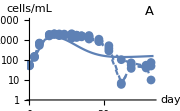
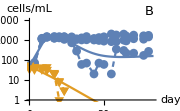
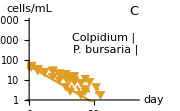
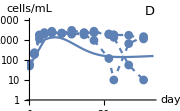
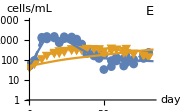
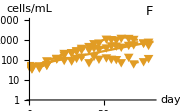
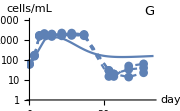
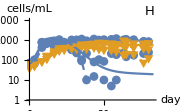
Increasing light intensity, μmol quanta m^-2 s^-1
-Graphics-        |  | Colpidium alone | Both species competing | P. bursaria alone
0 |   | -Graphics- | -Graphics- | -Graphics-
50 |   | -Graphics- | -Graphics- | -Graphics-
100 |   | -Graphics- | -Graphics- | -Graphics-
200 |   | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*plot fits*)
(*(Export[outputdirectory<>"mech-model-fits.svg",#];#)&@*)plots[model,rejoinpars[fitsave[model][[2]],testparspre[model],{c0,p0}]]
```

```mathematica
(*AIC of model fits*)
aic[fitsave[model][[1]],length,Length[pars[model]/.(#->Nothing&/@Join[{l},parskeep[model]])]]
```

2717.

```mathematica
(*R2 of model fits*)
R2[fitsave[model][[1]],SStot[True]]
```

0.454426

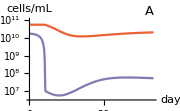
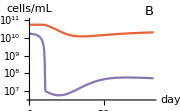
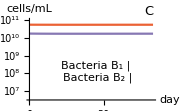
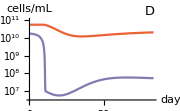
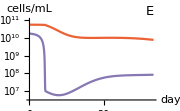
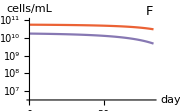
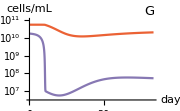
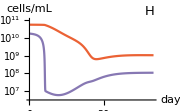
Increasing light intensity, μmol quanta m^-2 s^-1
-Graphics-        |  | Colpidium alone | Both species competing | P. bursaria alone
0 |   | -Graphics- | -Graphics- | -Graphics-
50 |   | -Graphics- | -Graphics- | -Graphics-
100 |   | -Graphics- | -Graphics- | -Graphics-
200 |   | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*bacteria trajectory plots*)
legendbacteria[i_]:=ListPlot[{{-.5,.48},{.47,.48},{1.5,.48}},Joined->True&@(ColorData[97][i]),PlotStyle->{Thick,ColorData[97][i]},PlotRange->{{0,1},{0,1}},Axes->None,ImageSize->25];
bacteriacols={4,5};
bacteriaplots[model_,parvals_]:=Style[
Row[{
Rotate[Column[{Style[Row[{"Increasing light intensity, μmol quanta m^-2 s^-1"}],FontFamily->fontfamily,14],
Style[Row[{ Graphics[{Thick,Arrowheads->Medium,Arrow[{{2.18,0},{1,0}}]},PlotRange->{-.02,.02},ImageSize->{Automatic,12}],"      "}],FontFamily->fontfamily,14]},Alignment->Center],π/2]," ",
Grid[Join[{Join[{"",""},choices["Treatment"]/.treatnames]},
Table[
Join[{Style[light,14,FontFamily->fontfamily]," "},Table[Show[{
(*plotdataplane[{treatment,light}],*)
With[{sol=sim[model][pars[model]/.Join[{l->light},inis[treatment],parvals],tmaxplot]},
LogPlot[Evaluate[{b1[t],b2[t]}/.sol],{t,0,tcropped},PlotRange->{Full,{10^6.5,10^11}},PlotStyle->({ColorData[97][#],Thick}&/@bacteriacols),Evaluate@plotdataplanestyle[treatment,light]]]
},
If[TrueQ[treatment=="P bur"∧light==0],Prolog->Inset[Framed[Style[Grid[{{"Bacteria B_1",legendbacteria[bacteriacols[[1]]]},{"Bacteria B_2",legendbacteria[bacteriacols[[2]]]}}],12],RoundingRadius->3,Background->White],Scaled[{.55,.36}]],{}],PlotRangeClipping->{{True,True},{False,False}}
],{treatment,choices["Treatment"]}
]],{light,choices["Light_Level"]}]],Spacings->{.3,{.3,1,.3,.3,.3}}(*,Frame->True*)]}],FontFamily->fontfamily];
(*(Export[outputdirectory<>"mech-model-fits-bacteria.svg",#];#)&@*)bacteriaplots[model,rejoinpars[fitsave[model][[2]],testparspre[model],{c0,p0}]]
```

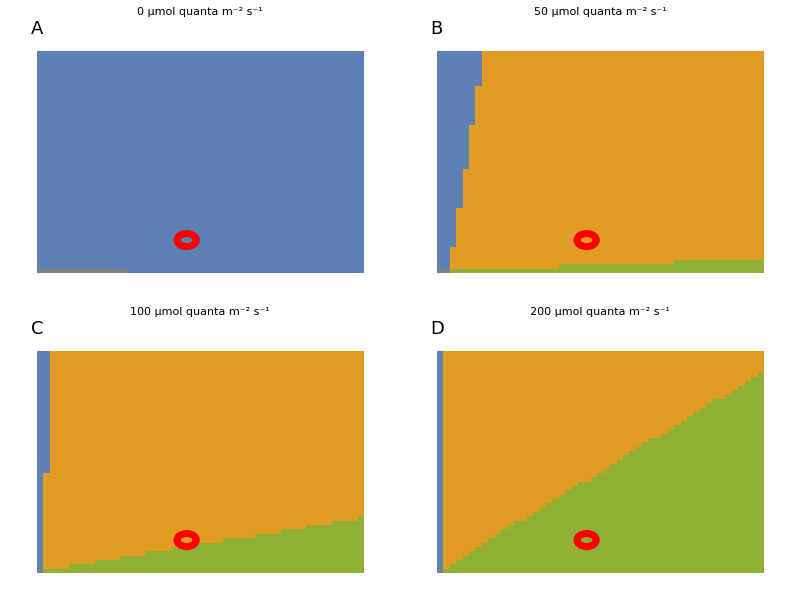
-Graphics- Colpidium    -Graphics- P. bursaria    -Graphics- Coexistence    -Graphics- None    -Graphics- Fitted bacteria parameters
 
-Graphics-

```mathematica
(*bacteria supply plots: outcome of competition in dependence of w1 and w2*)
(*legend*)
box[i_]:=Graphics[{If[NumberQ@i,ColorData[97][i],i],Rectangle[]},ImageSize->15];
legendbacteriasupply=Style[
Row[{box[1]," Colpidium    ",box[3]," P. bursaria    ",box[2]," Coexistence    ",box[Lighter@Gray]," None    " ,Graphics[{Red,Thickness[.15],Circle[]},ImageSize->15]," Fitted bacteria parameters"}]
,FontFamily->"Arial"];
(*letters for corners*)
panellabels2=#[[1]]->#[[2]]&/@Transpose[{Flatten[Table[light,{light,lights}],1],{"A","B","C","D"}}];
(*resolution of plots*)
finalstatesteps=50;
(*axis range for w1 and w2*)
w1max=2. 10^9;
w2max=2. 10^9;
(*function to determine the final outcome*)
(*time span for simulations*)
tmaxfinalstate=1000;
(*threshold for whether a populaiton is considered to be existing*)
finalstatethreshold=10^-3;
(*bin outcomes*)
finalstate[model_,parvals_,light_]:=With[{sol=sim[model][pars[model]/.Join[{l->light},inis["Comp"],parvals],tmaxfinalstate]},
Piecewise[{{1, c[tmaxfinalstate]>finalstatethreshold∧p[tmaxfinalstate]>finalstatethreshold}, {2, c[tmaxfinalstate]>finalstatethreshold∧p[tmaxfinalstate]<finalstatethreshold}, {3, c[tmaxfinalstate]<finalstatethreshold∧p[tmaxfinalstate]>finalstatethreshold}, {4, c[tmaxfinalstate]<finalstatethreshold∧p[tmaxfinalstate]<finalstatethreshold}}]/.sol];
(*function to create the supply plot*)
supplyplot[light_,axes1_,axes2_]:=Module[{data},
data=Table[finalstate[model,rejoinpars[Join[{w1->w1x,w2->w2x},fitsave[model][[2]]],testparspre[model],{c0,p0}],light],{w2x,0,w2max,w2max/finalstatesteps},{w1x,0,w1max,w1max/finalstatesteps}];
ArrayPlot[Reverse[data,{1}],ColorRules->{1->ColorData[97][2],2->ColorData[97][1],3->ColorData[97][3],4->Gray},FrameTicks->{{axes1,None},{axes2,None}},DataRange->{{0,w1max},{0,w2max}},AspectRatio->1,LabelStyle->12,FrameLabel->{Evaluate@If[TrueQ[axes1==All],"Bacteria supply w_1",None],Evaluate@If[TrueQ[axes2==All],"Bacteria supply w_2",None]},PlotLabel->Row[{light," μmol quanta m^-2 s^-1"}],ImageSize->300,ImagePadding->{{70,15},{50,20}}(*,ImagePadding->{{100,50},{50,50}}*),Epilog->{Red,Thickness[.017],Circle[{w1,w2}/.fitsave[model][[2]],.6 10^8],Black,Inset[Style[light/.panellabels2,18],Scaled[{.02,1.08}(*{.95,1.08}*)]]

},
PlotRangeClipping->False]
]
(*do the plots*)
(*(Export[outputdirectory<>"supply-plot.svg",#];#)&@*)Column[{legendbacteriasupply," ",Grid[{{supplyplot[0,All,All],supplyplot[50,All,All]},{supplyplot[100,All,All],supplyplot[200,All,All]}}]},Alignment->Center]
```

```mathematica
(*model with self-shading*)
model="huisman-weissing";
(*state variables*)
vars[model]={c,p,b};
(*define and run the model*)
sim[model][{
c0_,ac_,hc_,mc_,
p0_,ap_,hp_,mp_,
yc_,yp_,
w_,δ_,
k_,α_,l_
},tmax_]:=Module[{g,f,h,uc,lc,up,lp,ub},
f[a_,h_][x_]:=(a  x)/(1+a h x);
ub=w;
uc=f[ac,hc][b[t]] c[t];
lc=mc c[t];
up=f[ap,hp][b[t]] p[t];
lp=(p[t]- ( p[t]+(1/α )(Log[k+l]-Log[ⅇ^(α p[t]) k+l])))mp ;
NDSolve[
{
b'[t]==ub-uc-up-δ b[t],
c'[t]==yc uc-lc,
p'[t]==yp up-lp,
c[0]==c0,
p[0]==p0,
b[0]==w/δ
},
vars[model],
{t,0,tmax},MaxSteps->Infinity,Method->"Shooting"][[1]]];
(*parameters to initialize fitting*)
testparspre[model]={
c0->50,ac->.0001 ,hc-> 10^-7 ,mc->.3,
p0->50,ap->.001  ,hp->5  10^-7,mp->.5,
yc-> 10^-7,yp->10^-7,
w->10^9 ,δ->.2,
k->50,α->.001,l->50
};
(*parameters no to fit*)
parskeep[model]={c0,p0,yc,yp};
```

```mathematica
(*do the fit*)
AbsoluteTiming[fitsave[model]=fit[model,#>0&/@parstofit[model],parstofit[model],parskeep[model],Join[{ac->0.00009031644605480185,hc->1.8880224351941854*^-11,mc->0.5585399469960597,ap->0.000160744795155013,hp->1.9259847675103896*^-7,mp->0.524804818404551,w->4.196289246139989*^9,δ->0.037793437833028395,k->65.35115900401726,α->0.0020913140384195067},testpars[model]],True]]
```

{38.5893,{1177.49,{ac→0.0000866555,hc→1.21458×10^-11,mc→0.573425,ap→0.000160436,hp→1.8682×10^-7,mp→0.539587,w→4.47771×10^9,δ→0.038239,k→68.3675,α→0.00213055}}}

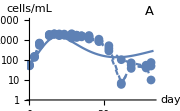
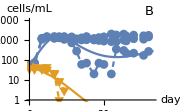
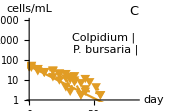
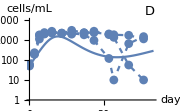
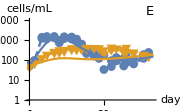
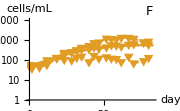
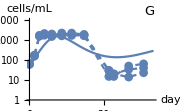
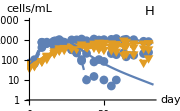
Increasing light intensity, μmol quanta m^-2 s^-1
-Graphics-        |  | Colpidium alone | Both species competing | P. bursaria alone
0 |   | -Graphics- | -Graphics- | -Graphics-
50 |   | -Graphics- | -Graphics- | -Graphics-
100 |   | -Graphics- | -Graphics- | -Graphics-
200 |   | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*show the fit*)
(*(Export[outputdirectory<>"h-w-model-fits.svg",#];#)&@*)plots[model,rejoinpars[fitsave[model][[2]],testparspre[model],{c0,p0}]]
```

```mathematica
(*AIC of model fits*)
aic[fitsave[model][[1]],length,Length[pars[model]/.(#->Nothing&/@Join[{l},parskeep[model]])]]
```

2771.47

```mathematica
(*R2 of model fits*)
R2[fitsave[model][[1]],SStot[True]]
```

0.416901

```mathematica
(*Lotka-Volterra model*)
model="lotka-volterra";
vars[model]={c,p};
sim[model][{
c0_,rc_,lc_,acp_,
p0_,r0_,rmax_,lp_,
apc_,
k_,l_
},tmax_]:=Module[{rp},
rp=r0+rmax l/(k+l);
NDSolve[
{
c'[t]==(rc-lc (c[t]+acp p[t])) c[t],
p'[t]==(rp-lp (p[t]+apc c[t])) p[t],
c[0]==c0,
p[0]==p0
},
vars[model],
{t,0,tmax},MaxSteps->Infinity,Method->"Shooting"][[1]]];
testparspre[model]={
c0->50,rc->1.2,lc->10^-3,acp->.05,
p0->50,r0->-.3,rmax->1,lp->10^-3.5,apc->.05,k->50,l->100};
parskeep[model]={c0,p0};
(*plots[model,testpars[model]]*)
```

```mathematica
fitc[model]=fitStages[model,True,Table[{"Colp",light},{light,lights}],tcropped,testpars[model],{rc,lc},{10^0>lc>10^-8}]
fitp[model]=fitStages[model,True,Table[{"P bur",light},{light,lights}],tcropped,testpars[model],{r0,rmax,lp,k},{rmax>0,k>0,10^0>lp>10^-8}]
fitcomp[model]=fitStages[model,True,Table[{"Comp",light},{light,lights}],tcropped,joinpars[joinpars[testpars[model],fitc[model][[2]]],fitp[model][[2]]],{acp,apc},{acp>0,apc>0}]
```

{529.744,{rc→1.05614,lc→0.00228565}}

{76.3855,{r0→-0.112909,rmax→0.363717,lp→0.0000379711,k→48.7403}}

{888.603,{acp→0.353193,apc→3.10904}}

```mathematica
(*the coexistence equilibrium is stable when this is > 1*)
```

```mathematica
acp apc /.fitcomp[model][[2]]
```

1.09809

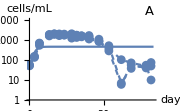
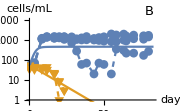
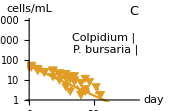
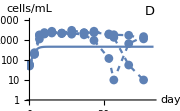
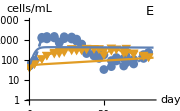
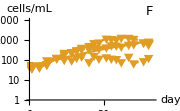
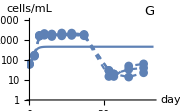
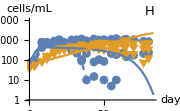
Increasing light intensity, μmol quanta m^-2 s^-1
-Graphics-        |  | Colpidium alone | Both species competing | P. bursaria alone
0 |   | -Graphics- | -Graphics- | -Graphics-
50 |   | -Graphics- | -Graphics- | -Graphics-
100 |   | -Graphics- | -Graphics- | -Graphics-
200 |   | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*(Export[outputdirectory<>"l-v-model-fits-two-stage.svg",#];#)&@*)plots[model,joinpars[joinpars[fitc[model][[2]],fitp[model][[2]]],fitcomp[model][[2]]]]
```

```mathematica
aic[fitc[model][[1]]+fitp[model][[1]]+fitcomp[model][[1]],length,8]
```

2977.17

```mathematica
(*R2 of model fits*)
R2[fitc[model][[1]]+fitp[model][[1]]+fitcomp[model][[1]],SStot[True]]
```

0.259799

```mathematica
(*fit L-V model in one stage*)
AbsoluteTiming[fitsaveONESTAGE[model]=fit[model,Join[#>0&/@(parstofit[model]/.r0->Nothing),{r0>-1}],parstofit[model],parskeep[model],Join[{rc->0.9235548503970105,lc->0.0017740025686773637,acp->0.6478248155154721,rmax->0.548565297773935,lp->0.0003046717009437276,apc->0.3838996050743106,k->52.17671784826194},testpars[model]](*testpars[model]*),True]]
```

{12.3433,{1236.97,{rc→0.913091,lc→0.00176493,acp→0.629055,r0→-0.120388,rmax→0.559839,lp→0.000300953,apc→0.364309,k→54.4631}}}

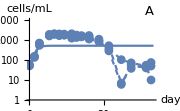
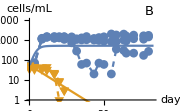
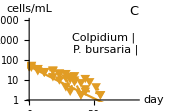
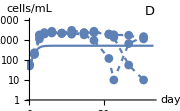
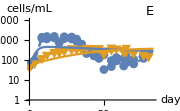
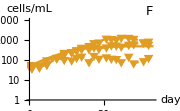
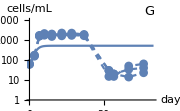
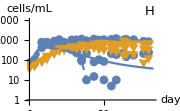
Increasing light intensity, μmol quanta m^-2 s^-1
-Graphics-        |  | Colpidium alone | Both species competing | P. bursaria alone
0 |   | -Graphics- | -Graphics- | -Graphics-
50 |   | -Graphics- | -Graphics- | -Graphics-
100 |   | -Graphics- | -Graphics- | -Graphics-
200 |   | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*show fits*)
(*(Export[outputdirectory<>"l-v-model-fits-one-stage.svg",#];#)&@*)plots[model,rejoinpars[fitsaveONESTAGE[model][[2]],testparspre[model],{c0,p0}]]
```

```mathematica
(*AIC*)
aic[fitsaveONESTAGE[model][[1]],length,8]
```

2810.79

```mathematica
(*R2 of model fits*)
R2[fitsaveONESTAGE[model][[1]],SStot[True]]
```

0.387445

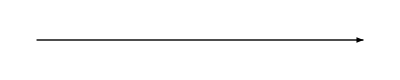
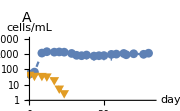
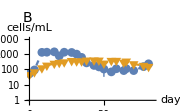
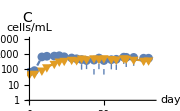
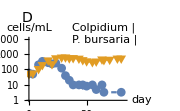
Increasing light intensity, μmol quanta m^-2 s^-1
       -Graphics-      
Population density    0 | 50 | 100 | 200
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Time | Time | Time | Time

```mathematica
(*additional plots showing data alone*)
legend[i_]:=ListPlot[{{-.5,.5},{.5,.5},{1.5,.5}},Joined->True,PlotMarkers->{Graphics`PlotMarkers[]⟦#⟦1⟧,1⟧,1.1#⟦2⟧}&@(plotmarkerstyles[[i]]),PlotStyle->{Dashing[.13],Thickness[.08],ColorData[97][i]},PlotRange->{{0,1},{0,1}},Axes->None,ImageSize->25];
transformlists[lists_]:=Map[{#[[1,1]],With[{points=#[[All,2]]},Around[Mean[points],If[Length[points]>1,StandardDeviation[points]/Sqrt@Length[points],0]]]}&,GatherBy[Flatten[lists,1],First]];
plotdataplanemean[{treatment_,light_}]:=ListLogPlot[Table[With[{lists=Table[Select[croptime[gettreatreplicates[{treatment,light,species,replicate}],tcropped],#1⟦2⟧≠0&],{replicate,choices["Replicate"]}]},
transformlists[lists]],{species,choices["Species"]}]/.{}->{{0,0}},Joined->True,PlotMarkers->Table[{Graphics`PlotMarkers[]⟦i⟦1⟧,1⟧,i⟦2⟧},{i,plotmarkerstyles}],PlotStyle->Table[{Dashing[.022],ColorData[97][i]},{i,2}],PlotRange->{{0,tmaxplot},{10^0,10^4}},AxesLabel->{"day","cells/mL"}];
(*(Export[outputdirectory<>"competition-row.svg",#];#)&@*)Style[
Column[{
Style[Row[{"Increasing light intensity, μmol quanta m^-2 s^-1"}],FontFamily->fontfamily,14],
Style[Row[{ "       ",Graphics[{Thick,Arrowheads->Medium,Arrow[{{1,0},{2.87,0}}]},PlotRange->{-.02,.02},ImageSize->{Automatic,12}],"      "}],FontFamily->fontfamily,14],
Row[{
Rotate[Style["Population density    ",FontFamily->fontfamily,11,Darker@Gray],π/2],
Grid[Transpose@Table[{Style[light,FontFamily->fontfamily,14],Show[{plotdataplanemean[{choices["Treatment"][[2]],light}]},Prolog->Inset[Style[light/.{0->"A",50->"B",100->"C",200->"D"},14],Scaled[{0,1.3}]],If[TrueQ[light==200],Epilog->Inset[Framed[Style[Grid[{{"Colpidium",legend[1]},{"P. bursaria",legend[2]}}],12],RoundingRadius->3],Scaled[{.78,1.05}]],{}],PlotRangeClipping->{{True,True},{False,False}},ImagePadding->{{Automatic,27},{Automatic,35}},ImageSize->Small],Style["Time",FontFamily->fontfamily,11,Darker@Gray]}
,{light,choices["Light_Level"]}]]}]
},Alignment->Center],FontFamily->fontfamily]
```

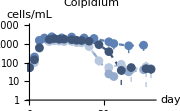
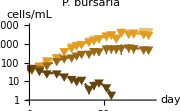
-Graphics-  Light intensity
μmol quanta m^-2 s^-1
-Graphics- | 0
-Graphics- | 50
-Graphics- | 100
-Graphics- | 200
  -Graphics-  Light intensity
μmol quanta m^-2 s^-1
-Graphics- | 0
-Graphics- | 50
-Graphics- | 100
-Graphics- | 200

```mathematica
speciesnames={"Colp"->"Colpidium","P bur"->"P. bursaria"};
colorsf[species_]:=Piecewise[{{ColorData[97][1], species=="Colp"}, {ColorData[97][2], species=="P bur"}}];
lightrowcolorsf[species_]:=Piecewise[{{{Lighter[Lighter[#]],Lighter[#],Identity[#],Darker[#]}, species=="Colp"}, {{Lighter[#],Identity[#],Darker[#],Darker@Darker[#]}, species=="P bur"}}]&[colorsf[species]];
legendlight[species_]:=Magnify[Framed[Style[Column[{"Light intensity","μmol quanta m^-2 s^-1",

Grid@Table[{Row[{ListPlot[{{-.5,.5},{.5,.5},{1.5,.5}},Joined->True,PlotMarkers->{Graphics`PlotMarkers[]⟦#⟦1⟧,1⟧,#⟦2⟧}&@(plotmarkerstyles[[species/.{"Colp"->1,"P bur"->2}]]),PlotStyle->{Dashed,Reverse[lightrowcolorsf[species]][[i]]},PlotRange->{{0,1},{0,1}},Axes->None,ImageSize->23]}],choices["Light_Level"][[i]]},{i,Length@choices["Light_Level"]}]},Alignment->Center],FontFamily->fontfamily],RoundingRadius->5],.8];
alllightsinglespeciesplot[species_]:=
ListLogPlot[Table[With[{lists=Table[Select[croptime[gettreatreplicates[{species,light,species,replicate}],tcropped],#1⟦2⟧≠0&],{replicate,choices["Replicate"]}]},
Sort[transformlists@lists,#1[[1]]<#2[[1]]&]],{light,Reverse@choices["Light_Level"]}]/.{}->{{0,0}},Joined->True,PlotMarkers->{Graphics`PlotMarkers[]⟦#⟦1⟧,1⟧,#⟦2⟧}&@(plotmarkerstyles[[species/.{"Colp"->1,"P bur"->2}]]),PlotStyle->({Dashing[.02],#}&/@lightrowcolorsf[species]),PlotRange->{{0,tmaxplot},{10^0,10^4}},AxesLabel->{"day","cells/mL"},ImageSize->Small,PlotLabel->Style[species/.speciesnames,12,Italic,FontFamily->fontfamily],IntervalMarkersStyle->lightrowcolorsf[species]];
(*(Export[outputdirectory<>"light-row.svg",#];#)&@*)Row[Table[Row[{alllightsinglespeciesplot[species],"  ",Column[{legendlight[species],"  "}]}],{species,choices["Species"]}],"      ",Alignment->Top]
```

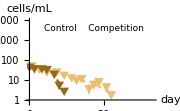
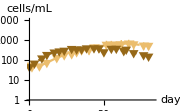
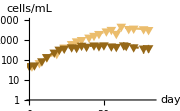
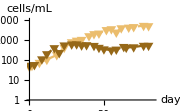
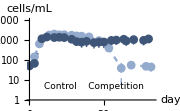
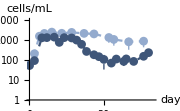
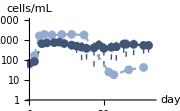
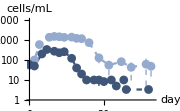
P. bursaria | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Colpidium | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | 0 | 50 | 100 | 200
       -Graphics-      
Increasing light intensity, μmol quanta m^-2 s^-1

```mathematica
plotmarkerstyles={{1,9},{5,11.5}};
colorsaloneVScomp[species_]:=({#@colorsf[species]}&/@{Lighter,Darker});
plotdataplanemeanaloneVScompetition[{species_,light_}]:=ListLogPlot[Table[With[{lists=Table[Select[croptime[gettreatreplicates[{treatment,light,species,replicate}],tcropped],#1⟦2⟧≠0&],{replicate,choices["Replicate"]}]},
transformlists[lists]],{treatment,{species,"Comp"}}]/.{}->{{0,0}},Joined->True,PlotMarkers->{Graphics`PlotMarkers[]⟦plotmarkerstyles[[#]]⟦1⟧,1⟧,plotmarkerstyles[[#]]⟦2⟧}&@Piecewise[{{1, species=="Colp"}, {2, species=="P bur"}}],PlotStyle->({Dashing[.022],#}&/@colorsaloneVScomp[species]),IntervalMarkersStyle->colorsaloneVScomp[species],PlotRange->{{0,tmaxplot},{10^0,10^4}},AxesLabel->{"day","cells/mL"},ImageSize->Small];
legendaloneVScompetition[species_]:=Style[Row[Table[Row[{Row[{ListPlot[{{-.5,.5},{.5,.5},{1.5,.5}},Joined->True,PlotMarkers->{Graphics`PlotMarkers[]⟦#⟦1⟧,1⟧,#⟦2⟧}&@(plotmarkerstyles[[species/.{"Colp"->1,"P bur"->2}]]),PlotStyle->{{Thickness[.11],Dashing[.185],colorsaloneVScomp[species][[i]]}},PlotRange->{{0,1},{0,1}},Axes->None,ImageSize->16]}],{"Control","Competition"}[[i]]},"  "],{i,2}],"     "],FontFamily->fontfamily,9];(*
Row[{legendaloneVScompetition/@choices["Species"]}]*)
(*(Export[outputdirectory<>"control-vs-competition.pdf",#];#)&@*)Style[
Column[{
Grid[Transpose[Join[{Rotate[Style[#,Italic,12,FontFamily->fontfamily],1/2π]&/@{"P. bursaria","Colpidium",""}},Table[Join[Table[Show[{plotdataplanemeanaloneVScompetition[{species,light}]},Epilog->If[light==0,Inset[legendaloneVScompetition[species],Scaled[Piecewise[{{{.52,.88}, species=="P bur"}, {{.52,.18}, species=="Colp"}}]]],{}]]
,{species,Reverse@choices["Species"]}],{Style[light,FontFamily->fontfamily,14]}],{light,choices["Light_Level"]}]]]],Style[Row[{ "       ",Graphics[{Thick,Arrowheads->Medium,Arrow[{{1,0},{2.87,0}}]},PlotRange->{-.02,.02},ImageSize->{Automatic,12}],"      "}],FontFamily->fontfamily,14],
Style[Row[{"Increasing light intensity, μmol quanta m^-2 s^-1"}],FontFamily->fontfamily,14]},Alignment->Center],FontFamily->fontfamily]
```